```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "../../plots/plots-105";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../runs/Trials/N9K9/81027575.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cMatOne[data[[1]]]
```

```mathematica
eig = Flatten@(Eigenvalues/@matdata[[All, 2]]);
```

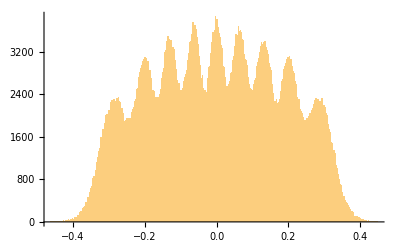

```mathematica
Histogram[eig, 300]
```

```mathematica
unitMats = RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], 100000];
```

```mathematica
unitEigs = Flatten[Eigenvalues/@unitMats];
```

```mathematica
unitMatsTrLess = (#-1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], 100000];
```

```mathematica
unitEigsTrLess = Flatten[Eigenvalues/@unitMatsTrLess];
```

```mathematica
plt2 = Histogram[{Standardize[eig],Standardize[unitEigsTrLess]}, 300, PDF,
ChartLegends->{"Simulation", "Traceless GUE"},
AxesLabel->{"eigenvalue", "PDF"},
PlotLabel->"Distribution of Eigenvalues of X1 across time",
ImageSize->600
];
```

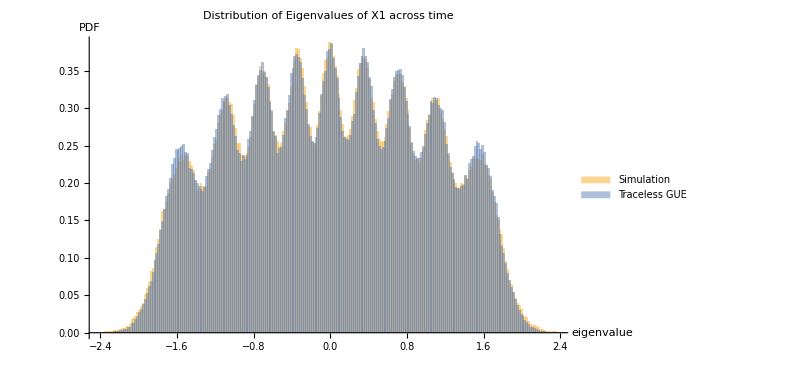

```mathematica
plt2
```

```mathematica
Export[plotsDir<>"/eigDist-TracelessGUE.pdf", Rasterize[plt2, ImageResolution->300, ImageSize->500]]
```

../../plots/plots-105/eigDist-TracelessGUE.pdf

```mathematica
plts=ParallelTable[Module[{},(
Print["Generating data n = "<>ToString@n];
obsSim[n]=Tr[MatrixPower[#,n]]&/@matdata[[All,2]]//Chop//Re;
obsUnitary[n]=Tr[MatrixPower[#,n]]&/@unitMatsTrLess//Chop//Re;
Print["Generating plot n = "<>ToString@n];
Histogram[{Standardize[obsSim[n]],Standardize[obsUnitary[n]]},3000,PDF,ImageSize->500,PlotLabel->"Tr[\!\(\*SuperscriptBox[\(X\),n]\)]; n = "<>ToString[n],ChartLegends->Placed[{"Simulation","Traceless GUE"},Bottom]]
)],{n,2,12}];

Print["Generating the full plot"];
plt=Framed[Column[{Style["Comparing with Traceless Gaussian Unitary Matrix Distribution",Darker@Blue,Bold,16],GraphicsGrid[ArrayReshape[plts,{4,3}],Frame->All,ImageSize->2000]},Alignment->Center],FrameMargins->10];

Print["Exporting"];
Export[plotsDir<>"/trXn-dist-tracelessGUE.pdf",Rasterize[plt,ImageResolution->300,ImageSize->500]];

Print["Done"];
```